FittedModel[355.419 ⅇ^(-0.00581698 ((«1»«1»)^2)]

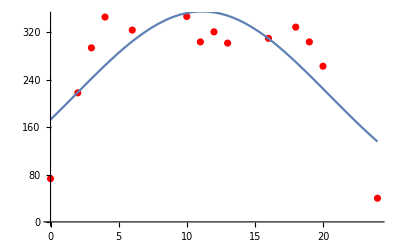

| Estimate | Standard Error | t-Statistic | P-Value
σ | 9.27121 | 1.30276 | 7.11658 | 0.0000195096
μ | 11.1324 | 0.910077 | 12.2323 | 9.54949×10^-8
A | 8259.75 | 881.752 | 9.36743 | 1.41469×10^-6

```mathematica
prompt = Sort[{{11,304},{0,73},{2,218},{16,310},{24,40},{18,329},{20,263},{19,304},{13,302},{12,321},{10,347},{4,346},{3,294},{6,324}}];
FindFit[prompt,A*1/(σ*Sqrt[2 π]) Exp[-(1/2) ((x-μ)/σ)^2],{σ,μ,A},x];
nlm =NonlinearModelFit[prompt,A*1/(σ*Sqrt[2 π]) Exp[-(1/2) ((x-μ)/σ)^2],{σ,μ,A},x]
Show[ListPlot[prompt,PlotStyle->Red],Plot[nlm[x], {x, 0, 24}]]
nlm["ParameterTable"]
```

```mathematica
nlm[61]
```

0.000185536